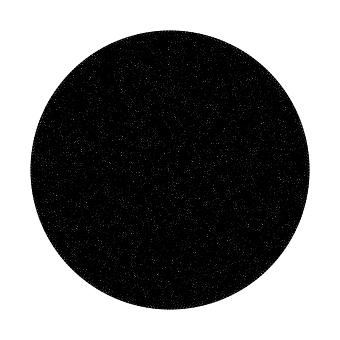

Number of Elements:21402

```mathematica
Needs["NDSolve`FEM`"]
R=10;
maxCellMeasure=0.025;
Ω=Disk[{0,0},R];
mesh=ToElementMesh[Ω,"MeshOrder"->1,MaxCellMeasure->maxCellMeasure,MeshQualityGoal-> 1,"NodeReordering"-> True,"IncludePoints"->{{0.,0.}}];
coorVerticesXY=mesh["Coordinates"];
coorVerticesXYZ=MapThread[Append,{coorVerticesXY,ConstantArray[0,Length[coorVerticesXY]]}];
conn=mesh["MeshElements"][[1]][[1]];
Show[Graphics[{EdgeForm[Black],FaceForm[],GraphicsComplex[coorVerticesXY,Polygon[conn]]}]]
numberElements=Dimensions[conn,1][[1]];
Labeled["Number of Elements:",numberElements]
```

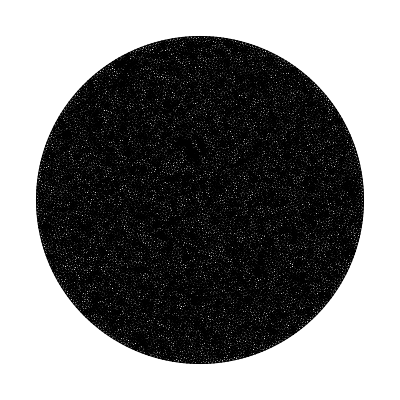

```mathematica
mm=Show[Graphics[{EdgeForm[Black],FaceForm[],GraphicsComplex[coorVerticesXY,Polygon[conn]]}]]
```

```mathematica
Export[NotebookDirectory[]<>"CircleMesh-7.obj",mm,"Binary"-> True]
```

/Users/bricelecampion/Documents/Work/Geomechanics/Codes/minimalFE/mma-stuff/CircleMesh-7.obj

```mathematica
665*3
```

1995

```mathematica
(Norm[#]&/@ mesh[[1]] )// Min
```

0.11355

```mathematica
mesh[[1]]//Length
```

134624

```mathematica
90/15
```

6

```mathematica
56/11
```

```mathematica
66/8
```

33/4